```mathematica
Approx[ x_, t_ ] := -MangoldtLambda[ n ] / 2 / Log[ n ] +  N[ 2Re[ Sum[ ExpIntegralEi[ ZetaZero[ k ] Log[ x ]], { k, 1, t }]]] - NIntegrate[ 1 / (( y ^ 3 - y )  Log[ y ]), { y, x, Infinity }] + Log[ 2 ]
D2Approx[ n_, j_ ] := ( -1 ) ^ j  ( 1 - n Sum[( -Log[ n ]) ^ k / ( k! ), { k, 0, j - 1 }])
Dhyp[ n_, k_, a_ ] := Sum[ Binomial[ k, j ] Dhyp[ n / ( m ^ ( k - j )), j, m + 1 ],{ m, a, n ^ ( 1 / k )}, { j, 0, k - 1 }]
Dhyp[ n_, 1, a_ ] := If[ n < a, 0, Floor[ n ] - a + 1 ] ; Dhyp[ n_, 0, a_ ] := 1
dhyp[ n_, k_, a_ ] := dhyp[ n, k, a ] = Dhyp[ n, k, a ] - Dhyp[ n - 1, k, a ]
LinnikApprox[  n_ ] :=  Log[ Log[ n ]] + EulerGamma + Sum[ ( -1 ) ^ ( k + 1 ) / k  (D2Approx[ n, k ] - Dhyp[ n, k, 2 ]), { k, 2, 100 }]
```

```mathematica
Table[{n,N[Approx[n,200]], N[LinnikApprox[n]]},{n,2,100}]//TableForm
```

2 | 0.0404408 | 0.0451638
3 | 0.168095 | 0.163589
4 | 0.470302 | 0.467585
5 | 0.137339 | 0.134588
6 | 0.716942 | 0.722222
7 | 0.252888 | 0.257052
8 | 0.420725 | 0.420385
9 | 0.387728 | 0.387904
10 | 0.829857 | 0.832266
11 | 0.267622 | 0.257676
12 | 0.641954 | 0.667214
13 | 0.050246 | 0.0632146
14 | 0.44657 | 0.447492
15 | 0.810561 | 0.821492
16 | 0.927181 | 0.936383
17 | 0.28454 | 0.293131
18 | 0.645275 | 0.642541
19 | -0.0116518 | -0.0147075
20 | 0.323054 | 0.321967
21 | 0.650298 | 0.653064
22 | 0.974469 | 0.979019
23 | 0.306377 | 0.300214
24 | 0.612812 | 0.616982
25 | 0.433014 | 0.429623
26 | 0.723349 | 0.738401
27 | 0.731966 | 0.71022
28 | 1.00717 | 1.01196
29 | 0.29671 | 0.310485
30 | 0.594435 | 0.605966
31 | -0.102194 | -0.101436
32 | 0.016244 | -0.0115745
33 | 0.294331 | 0.275685
34 | 0.567287 | 0.560464
35 | 0.842675 | 0.842878
36 | 1.12052 | 1.12303
37 | 0.417993 | 0.40102
38 | 0.659374 | 0.676936
39 | 0.927158 | 0.950862
40 | 1.27621 | 1.22288
41 | 0.466328 | 0.493056
42 | 0.769206 | 0.761465
43 | 0.0394584 | 0.0281692
44 | 0.253858 | 0.293229
45 | 0.573268 | 0.556702
46 | 0.827592 | 0.818641
47 | 0.0877267 | 0.0790972
48 | 0.329784 | 0.338117
49 | 0.0726235 | 0.0957474
50 | 0.370153 | 0.35203
51 | 0.620274 | 0.607005
52 | 0.832117 | 0.860712
53 | 0.109475 | 0.113187
54 | 0.397738 | 0.364464
55 | 0.622202 | 0.614578
56 | 0.860014 | 0.86356
57 | 1.09222 | 1.11144
58 | 1.30476 | 1.35824
59 | 0.584248 | 0.604005
60 | 0.848747 | 0.848746
61 | 0.113974 | 0.092492
62 | 0.394565 | 0.335268
63 | 0.604427 | 0.577097
64 | 0.675077 | 0.651335
65 | 0.912491 | 0.891336
66 | 1.12267 | 1.13045
67 | 0.40463 | 0.368709
68 | 0.680656 | 0.606119
69 | 0.872629 | 0.842704
70 | 1.05371 | 1.07848
71 | 0.297926 | 0.313464
72 | 0.524036 | 0.547673
73 | -0.244028 | -0.218877
74 | 0.019978 | 0.0138289
75 | 0.238055 | 0.245805
76 | 0.486408 | 0.477066
77 | 0.728116 | 0.707625
78 | 0.926788 | 0.937496
79 | 0.168923 | 0.166691
80 | 0.40779 | 0.395224
81 | 0.367812 | 0.373105
82 | 0.591654 | 0.600347
83 | -0.159223 | -0.173039
84 | 0.056158 | 0.0529582
85 | 0.227667 | 0.278349
86 | 0.491898 | 0.503143
87 | 0.777028 | 0.727352
88 | 0.971057 | 0.950984
89 | 0.164343 | 0.174049
90 | 0.3773 | 0.396556
91 | 0.589805 | 0.618515
92 | 0.852074 | 0.839934
93 | 1.07631 | 1.06082
94 | 1.2574 | 1.28118
95 | 1.50417 | 1.50103
96 | 1.77634 | 1.72037
97 | 0.950746 | 0.939214
98 | 1.07983 | 1.15756
99 | 1.38151 | 1.37542
100 | 1.66304 | 1.59281

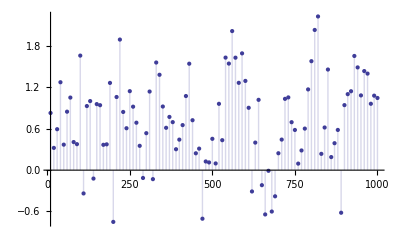

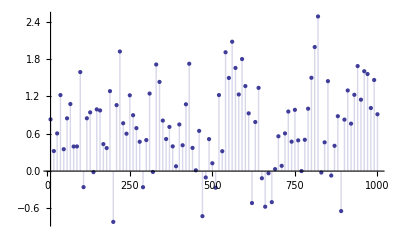

```mathematica
DiscretePlot[Approx[n,200],{n,10,1000,10}]//TableForm
DiscretePlot[LinnikApprox[n],{n,10,1000,10}]//TableForm
```

```mathematica
Table[{n,N[Approx[n,200]], N[LinnikApprox[n]]},{n,2,100}]//TableForm
```

2 | 0.0404408 | 0.0451638
3 | 0.168095 | 0.163589
4 | 0.470302 | 0.467585
5 | 0.137339 | 0.134588
6 | 0.716942 | 0.722222
7 | 0.252888 | 0.257052
8 | 0.420725 | 0.420385
9 | 0.387728 | 0.387904
10 | 0.829857 | 0.832266
11 | 0.267622 | 0.257676
12 | 0.641954 | 0.667214
13 | 0.050246 | 0.0632146
14 | 0.44657 | 0.447492
15 | 0.810561 | 0.821492
16 | 0.927181 | 0.936383
17 | 0.28454 | 0.293131
18 | 0.645275 | 0.642541
19 | -0.0116518 | -0.0147075
20 | 0.323054 | 0.321967
21 | 0.650298 | 0.653064
22 | 0.974469 | 0.979019
23 | 0.306377 | 0.300214
24 | 0.612812 | 0.616982
25 | 0.433014 | 0.429623
26 | 0.723349 | 0.738401
27 | 0.731966 | 0.71022
28 | 1.00717 | 1.01196
29 | 0.29671 | 0.310485
30 | 0.594435 | 0.605966
31 | -0.102194 | -0.101436
32 | 0.016244 | -0.0115745
33 | 0.294331 | 0.275685
34 | 0.567287 | 0.560464
35 | 0.842675 | 0.842878
36 | 1.12052 | 1.12303
37 | 0.417993 | 0.40102
38 | 0.659374 | 0.676936
39 | 0.927158 | 0.950862
40 | 1.27621 | 1.22288
41 | 0.466328 | 0.493056
42 | 0.769206 | 0.761465
43 | 0.0394584 | 0.0281692
44 | 0.253858 | 0.293229
45 | 0.573268 | 0.556702
46 | 0.827592 | 0.818641
47 | 0.0877267 | 0.0790972
48 | 0.329784 | 0.338117
49 | 0.0726235 | 0.0957474
50 | 0.370153 | 0.35203
51 | 0.620274 | 0.607005
52 | 0.832117 | 0.860712
53 | 0.109475 | 0.113187
54 | 0.397738 | 0.364464
55 | 0.622202 | 0.614578
56 | 0.860014 | 0.86356
57 | 1.09222 | 1.11144
58 | 1.30476 | 1.35824
59 | 0.584248 | 0.604005
60 | 0.848747 | 0.848746
61 | 0.113974 | 0.092492
62 | 0.394565 | 0.335268
63 | 0.604427 | 0.577097
64 | 0.675077 | 0.651335
65 | 0.912491 | 0.891336
66 | 1.12267 | 1.13045
67 | 0.40463 | 0.368709
68 | 0.680656 | 0.606119
69 | 0.872629 | 0.842704
70 | 1.05371 | 1.07848
71 | 0.297926 | 0.313464
72 | 0.524036 | 0.547673
73 | -0.244028 | -0.218877
74 | 0.019978 | 0.0138289
75 | 0.238055 | 0.245805
76 | 0.486408 | 0.477066
77 | 0.728116 | 0.707625
78 | 0.926788 | 0.937496
79 | 0.168923 | 0.166691
80 | 0.40779 | 0.395224
81 | 0.367812 | 0.373105
82 | 0.591654 | 0.600347
83 | -0.159223 | -0.173039
84 | 0.056158 | 0.0529582
85 | 0.227667 | 0.278349
86 | 0.491898 | 0.503143
87 | 0.777028 | 0.727352
88 | 0.971057 | 0.950984
89 | 0.164343 | 0.174049
90 | 0.3773 | 0.396556
91 | 0.589805 | 0.618515
92 | 0.852074 | 0.839934
93 | 1.07631 | 1.06082
94 | 1.2574 | 1.28118
95 | 1.50417 | 1.50103
96 | 1.77634 | 1.72037
97 | 0.950746 | 0.939214
98 | 1.07983 | 1.15756
99 | 1.38151 | 1.37542
100 | 1.66304 | 1.59281